#### Initialize (Set parameters, functions. Import images)

```mathematica
dir=NotebookDirectory[]
```

L:\users\xing\image\Xing\Xing\Kexi project\paper submit\NCB\NCB paper fourth round\Raw data\chromosome trace\control\

```mathematica
scale=0.5930474(*μm/pixel*);Δt=150(*second*);filename="052418_control_1";
```

```mathematica
ggrid[colnum_:10,imglist_,imgsz_:960]:=GraphicsGrid[If[Mod[Length[#],colnum]≠0,Append[Partition[#,colnum],Take[#,-Mod[Length[#],colnum]]],Partition[#,colnum]],ItemAspectRatio->1/Divide@@ImageDimensions[#[[1]]],Spacings->5,ImageSize->imgsz]&@imglist
```

```mathematica
img=Import[dir<>filename<>".tif"];
```

```mathematica
imgdna=(Transpose@Partition[img,2])[[1]];
```

```mathematica
di=ImageDimensions@First@imgdna
```

{148,155}

```mathematica
ggrid@(ImageAdjust/@imgdna)
```

-Graphics-

#### Image processing

Obtain DNA position

```mathematica
bdnaimg=Table[DeleteSmallComponents@Binarize[GaussianFilter[imgdna[[i]],6],0.05],{i,Length@imgdna}];ggrid@bdnaimg
```

-Graphics-

```mathematica
dnacor=Table[Last/@ComponentMeasurements[bdnaimg[[i]],"Centroid"],{i,Length@bdnaimg}]
```

{{{75.1196,81.433}},{{75.1982,81.9509}},{{76.1858,82.4899}},{{77.0284,81.6446}},{{77.4815,80.5706}},{{78.0772,81.799}},{{77.8037,81.2383}},{{77.5215,81.2003}},{{78.6726,81.5896}},{{79.3969,81.4388}},{{78.1082,81.3402}},{{77.8269,81.657}},{{78.601,81.8339}},{{79.8151,81.8103}},{{78.9967,81.5877}},{{79.0954,81.0237}},{{79.9926,81.3118}},{{79.5979,80.9992}},{{79.4275,81.0535}},{{80.1127,80.8203}},{{80.7829,81.3438}},{{81.645,80.3583}},{{82.5901,80.7092}},{{83.3165,79.9661}},{{83.8413,79.6476}},{{83.87,79.311}},{{84.037,79.0611}},{{84.7937,80.8614}},{{82.9991,80.483}},{{82.5308,80.8048}},{{83.9387,81.1252}},{{84.2931,81.5213}},{{84.4258,81.2504}},{{83.615,81.2652}},{{84.8134,81.7116}},{{85.6997,82.4271}},{{86.4412,81.3616}},{{87.2466,81.1241}},{{87.9637,81.6869}},{{89.4984,82.5879}},{{89.8114,82.4952}},{{90.4874,82.8002}},{{91.7657,82.8884}},{{93.1109,83.1977}},{{94.1734,82.6273}},{{94.3274,83.0195}},{{95.6166,83.1453}},{{95.942,83.4451}},{{97.3805,83.2169}}}

```mathematica
Length/@dnacor
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
```

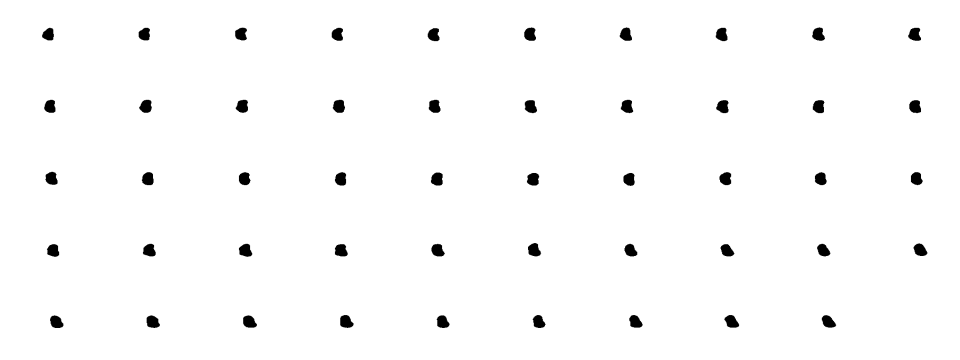

```mathematica
ggrid@(HighlightImage@@@(Transpose@{ImageAdjust/@imgdna,Transpose@{bdnaimg,dnacor}}))
```

```mathematica
cordat=Partition[Flatten@dnacor,2]
```

{{75.1196,81.433},{75.1982,81.9509},{76.1858,82.4899},{77.0284,81.6446},{77.4815,80.5706},{78.0772,81.799},{77.8037,81.2383},{77.5215,81.2003},{78.6726,81.5896},{79.3969,81.4388},{78.1082,81.3402},{77.8269,81.657},{78.601,81.8339},{79.8151,81.8103},{78.9967,81.5877},{79.0954,81.0237},{79.9926,81.3118},{79.5979,80.9992},{79.4275,81.0535},{80.1127,80.8203},{80.7829,81.3438},{81.645,80.3583},{82.5901,80.7092},{83.3165,79.9661},{83.8413,79.6476},{83.87,79.311},{84.037,79.0611},{84.7937,80.8614},{82.9991,80.483},{82.5308,80.8048},{83.9387,81.1252},{84.2931,81.5213},{84.4258,81.2504},{83.615,81.2652},{84.8134,81.7116},{85.6997,82.4271},{86.4412,81.3616},{87.2466,81.1241},{87.9637,81.6869},{89.4984,82.5879},{89.8114,82.4952},{90.4874,82.8002},{91.7657,82.8884},{93.1109,83.1977},{94.1734,82.6273},{94.3274,83.0195},{95.6166,83.1453},{95.942,83.4451},{97.3805,83.2169}}

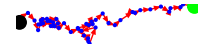

```mathematica
Graphics[{{Red,Arrowheads[Medium],Arrow/@Partition[cordat,2,1]},{Blue,Point/@cordat},{Black,PointSize[0.05],Point@(First@cordat)},{Green,PointSize[0.05],Point@(Last@cordat)}}]
```

```mathematica
vec=First@cordat-Last@cordat;nvec=vec/(Norm@vec);
```

```mathematica
dis=Table[(cordat[[i]]-Last@cordat).nvec,{i,Length@cordat}]
```

{22.3323,22.2125,21.1851,20.4127,20.0468,19.3549,19.6723,19.9566,18.7781,18.0681,19.3606,19.6158,18.83,17.6216,18.4552,18.4019,17.4845,17.903,18.0684,17.404,16.6942,15.9136,14.9434,14.2787,13.7811,13.7794,13.6328,12.7347,14.5538,14.9949,13.566,13.181,13.0705,13.8774,12.6472,11.7066,11.0526,10.2687,9.50898,7.9072,7.60259,6.90442,5.6231,4.25756,3.244,3.05912,1.76402,1.41569,0.}

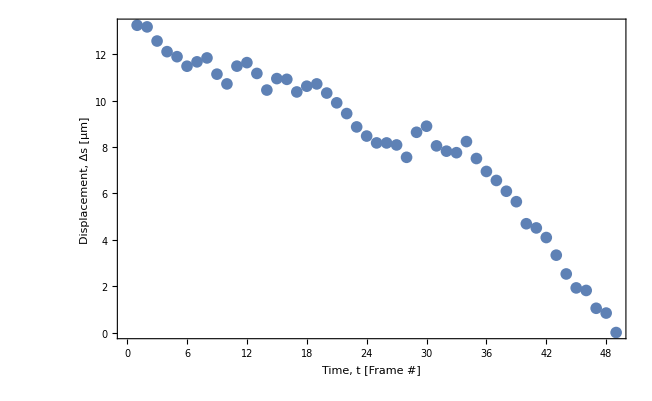

```mathematica
ListPlot[scale dis,Frame->True,FrameLabel->{"Time, t [Frame #]","Displacement, Δs [μm]"},BaseStyle->Large]
```

```mathematica
disreal=Transpose@{Δt (Range[Length@cordat]-1)/60.0,scale dis}
```

{{0.,13.2441},{2.5,13.1731},{5.,12.5637},{7.5,12.1057},{10.,11.8887},{12.5,11.4784},{15.,11.6666},{17.5,11.8352},{20.,11.1363},{22.5,10.7153},{25.,11.4818},{27.5,11.6331},{30.,11.1671},{32.5,10.4505},{35.,10.9448},{37.5,10.9132},{40.,10.3691},{42.5,10.6173},{45.,10.7154},{47.5,10.3214},{50.,9.90046},{52.5,9.43754},{55.,8.86217},{57.5,8.46796},{60.,8.17284},{62.5,8.17184},{65.,8.08492},{67.5,7.5523},{70.,8.63109},{72.5,8.8927},{75.,8.04528},{77.5,7.81698},{80.,7.7514},{82.5,8.22997},{85.,7.50039},{87.5,6.94257},{90.,6.55471},{92.5,6.08983},{95.,5.63928},{97.5,4.68935},{100.,4.50869},{102.5,4.09465},{105.,3.33476},{107.5,2.52493},{110.,1.92385},{112.5,1.81421},{115.,1.04615},{117.5,0.839569},{120.,0.}}

```mathematica
Export[dir<>filename<>".csv",disreal]
```

L:\users\xing\image\Xing\Xing\Kexi project\paper submit\NCB\NCB paper fourth round\Raw data\chromosome trace\control\052418_control_1.csv

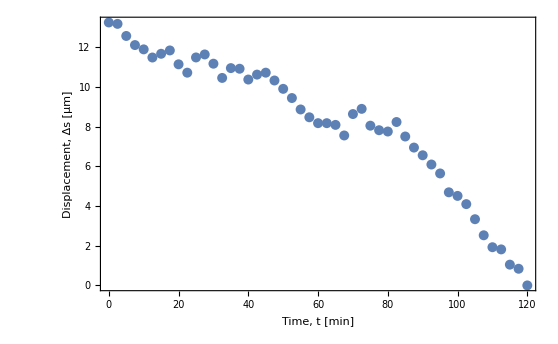

```mathematica
fig=ListPlot[disreal,Frame->True,FrameLabel->{"Time, t [min]","Displacement, Δs [μm]"},BaseStyle->Large]
```

```mathematica
fform=Fit[disreal,{1,x},x]
```

13.8791-0.0939234 x

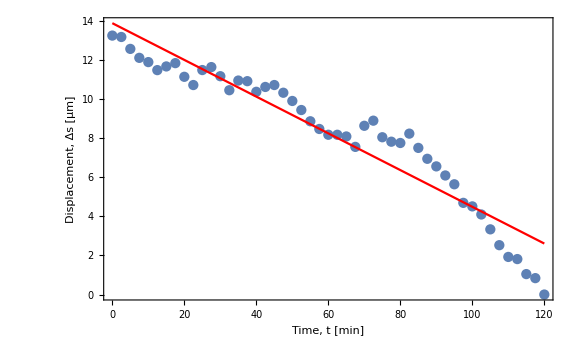

```mathematica
Show[fig,Plot[fform,{x,0,First@(Last@disreal)},PlotStyle->Red],PlotRange->All]
```

```mathematica
vel=60 scale (Norm@vec)/(Δt (Length@cordat-1))
```

0.110368

```mathematica
-fform[[2]]/x
```

0.0939234